CIP 1.2 - Scientific Data Analysis with integrated Packages for Curve Fitting, Clustering and Machine Learning

This tutorial provides an introduction and overview of CIP 1.2 that complements the discussion in textbook

Achim Zielesny, From Curve Fitting to Machine Learning: An illustrative Guide to scientific Data Analysis and Computational Intelligence, Berlin 2011. (Springer: Intelligent Systems Reference Library, Volume 18).

CIP 1.2 is available at http://www.gnwi.de.

Curve fitting, data smoothing, clustering and machine learning are important computational optimization techniques for scientific data analysis. To alleviate and unify these data analysis workflows a set of integrated packages (CIP) based on the Mathematica computing platform provides comfortable high-level functions and corresponding data structures. The packages may be easily extended or tailored for specific needs.

## Introduction

The interplay between experiment and theory is a key driving force of modern science. Experimental data do only have meaning in the light of a particular theoretical model or at least a theoretical background. Reversely, theoretical considerations may be logically consistent as well as intellectually elegant: Without experimental evidence they are a mere exercise of thought no matter how difficult they are. Data analysis is a connector between experiment and theory: Its techniques advise possibilities of model extraction as well as model testing with experimental data.

Theory-driven research areas like physical chemistry or biophysics do often experimentally study a scientific quantity of interest (y) in dependence of another quantity (x).  The dependency in question is theoretically described by a model function y=f(x), e.g. a straight line y=f(x)=a_1+a_2 x. Often only the structural form of f(x) is known (e.g. that f is a straight line) but not the values of its parameters (e.g. the values of a_1 and a_2). Curve fitting methods allow to estimate the parameter values of a known structural model function on the basis of experimental data with errors that follow a specific statistical distribution (which often is the normal distribution). Pure data smoothing techniques may be applied if even the structural form of y=f(x) is unknown.

With increasing complexity of the natural system under investigation a quantitative theoretical treatment becomes more and more difficult, e.g. contemporary molecular science fails to predict biological activities of new molecular entities or the properties of new material’s compositions. To still achieve at least an approximate quantitative description of chemical-structure-activity/property relationships (QSAR/QSPR) of the form activity/property=f(descriptor 1,descriptor 2,descriptor 3,...) a model function f may be solely constructed on the basis of adequate structural descriptors and corresponding experimental activities/properties - a task that is at heart of machine learning. The distribution of chemical structure related descriptors within the descriptor space itself may be investigated by clustering techniques, e.g. to select representatives for training and test sets which are mandatory for the validation of machine learning results.

The sketched data analysis tasks can be traced to mathematical (constrained or unconstrained, linear or non-linear) optimization problems which may be tackled with Mathematica’s built-in algorithms.

## CIP Description

CIP (Computational Intelligence Packages) is an open-source high-level function library which mainly exploits Mathematica’s built-in algorithmic and graphical capabilities to support scientific data analysis workflows for (non-linear) curve fitting and data smoothing (with cubic splines), clustering (k-medoids, ART-2a) and machine learning (multiple linear/polynomial regression, 3-layer feed-forward perceptron-type neural networks and support vector machines). In addition the packages provide several heuristics for the selection of training and test data or methods to estimate the relevance of data input components. A number of useful auxiliary functions and experimental data for testing purposes complement the offer.

For ease of use CIP-based workflows follow an intuitive and unified Get-Fit-Show/Calculate scheme: With Get methods data are retrieved from the ExperimentalData package or simulated with the CalculatedData package (alternatively data with an adequate data structure may be provided from any source). The data are then submitted to a Fit method of the CurveFit, Cluster, MLR, MPR, SVM or Perceptron packages to perform a corresponding optimization procedure. The result of a Fit method is a comprehensive info data structure, e.g. a curveFitInfo, clusterInfo, mlrInfo, mprInfo, svmInfo or perceptronInfo. This info data structure may then be passed to Show methods for multiple evaluation purposes like visual inspection of the goodness of fit or to Calculate methods for model related calculations. Similar functions of different packages are denoted in a similar manner for convenient applicability and intuitive method changes. Function signatures do mainly contain only method-dependent structural hyper-parameters (like the number of hidden neurons for perceptrons or the kernel function for support vector machines) whereas technical control parameters (like the maximum number of iterations) may be changed via options if necessary. Some CIP packages do only perform auxiliary tasks like the Graphics package that provides standardized 2D and 3D diagrams.

The CIP design goals were neither maximum speed nor minimum memory consumption but a unified definition of robust high-level functions for scientific data analysis workflows. Thus CIP is not a generally optimized and maximum efficient library for any scientific application although it may and is practically utilized in many operational areas (see individual package comments below). Since CIP is LGPL open-source the library may be used as a starting point for customized and tailored extensions, e.g. an implementation of a multicore processor support to increase computational speed (many CIP operations are ideally suited for parallel operation).

CIP consists of 11 integrated packages:

Utility - basic package that collects several general functions (like GetMeanSquaredError which is used by all machine learning related packages) to decrease redundant code.

ExperimentalData - provides test data. It makes use of the packages Utility, DataTransformation and CurveFit.

DataTransformation - performs internal data transformations for different purposes, e.g. all data that are passed to a machine learning method are scaled before a Fit operation. It uses the Utility package.

Graphics - tailors Mathematica’s built-in graphical functions for diagrams and graphical representations. It uses the Utility and DataTransformation packages.

CalculatedData - complements the ExperimentalData package with methods for the generation of simulated data like normally distributed xy-error data around a defined function, e.g. for the test of curve fitting workflows. It uses methods from the Utility and DataTransformation packages.

CurveFit - tailors Mathematica’s built-in curve fitting method (NonlinearModelFit) for least-squares minimization and adds a smoothing cubic splines support. Since NonlinearModelFit is an algorithmic state-of-the-art implementation for curve fitting the CurveFit package is well-suited for professional data analysis purposes. It uses the Utility, Graphics, DataTransformation and CalculatedData packages.

Cluster - tailors Mathematica’s built-in FindClusters method for clustering purposes and adds an adaptive resonance theory (ART-2a) support. FindClusters is an algorithmic state-of-the-art implementation for k-medoids clustering. The package uses the Utility, Graphics and DataTransformation packages.

MLR/MPR - tailor Mathematica’s built in Fit method for multiple linear or polynomial regression (MLR/MPR) which is an algorithmic state-of-the-art implementation. The packages use the Utility, Graphics, DataTransformation and Cluster packages.

Perceptron - provides optimization algorithms for three-layer perceptron-type neural networks. It utilizes Mathematica’s FindMinimum (ConjugateGradient) or NMinimize (DifferentialEvolution) methods for unconstrained minimization tasks. The package also provides a backpropagation-plus-momentum minimization and a genetic-algorithm-based minimization. Although the quality of the minimization algorithms is state-of-the-art the specific calculation setup contains non-optimum redundancies that decrease performance and increase memory consumption. It uses the Utility, Graphics, DataTransformation and Cluster packages.

SVM - provides constrained optimization algorithms for support vector machines (SVM). It utilizes Mathematica’s FindMaximum (InteriorPoint) or NMaximize (DifferentialEvolution) methods for constrained optimization tasks. Although these algorithms are robust they do not exploit any specifics of the support vector objective function to increase convergence speed etc. The package uses the Utility, Graphics, DataTransformation and Cluster packages.

The CIP folder with the 11 package (.m) files should be located in Mathematica’s “AddOns\Applications” directory. The CIP folder may be downloaded as a ZIP-file at the website given in the references. This website also provides additional information (like notebook files with tutorials) and a CIP user forum for discussion.

## Data Analysis Workflows

In the following CIP-based data analysis workflows are demonstrated that describe common applications of these packages. More examples and applications are provided in the textbook and on the website cited in the references.

### Curve Fitting and Data Smoothing

Curve fitting and data smoothing try to construct a model function y=f(x) for statistically independent and normally distributed xy-error data where the structure of the model function is known (curve fitting) or unknown (data smoothing). A xy-error data structure consists of xy-error triples (x_i,y_i,σ_i) with an argument value x_i, a corresponding dependent value y_i and the statistical error σ_i of the y_i value. The xy-error data structure is a list of sublists where each sublist represents a single xy-error triple, e.g.

```mathematica
xyErrorTriple1={Subscript[x, 1],Subscript[y, 1],Subscript[σ, 1]};
xyErrorTriple2={Subscript[x, 2],Subscript[y, 2],Subscript[σ, 2]};
xyErrorTriple3={Subscript[x, 3],Subscript[y, 3],Subscript[σ, 3]};
xyErrorData={xyErrorTriple1,xyErrorTriple2,xyErrorTriple3}
```

{{x_1,y_1,σ_1},{x_2,y_2,σ_2},{x_3,y_3,σ_3}}

With the GetXyErrorData method of the CalculatedData package

```mathematica
<<CIP`CalculatedData`
```

50 independent and normally distributed xy-error triples

```mathematica
numberOfData=50;
```

with an absolute error (standard deviation) of 0.5

```mathematica
standardDeviationRange={0.5,0.5};
```

are generated around the non-linear bell-shaped function

y=f(x)=1/2 x +3exp{-(x-4)^2}

```mathematica
pureOriginalFunction=Function[x,0.5*x+3.*Exp[-(x-4.)^2]];
```

in the argument range [1,7]

```mathematica
xMin=1.;
xMax=7.;
argumentRange={xMin,xMax};

xyErrorData=CIP`CalculatedData`GetXyErrorData[
	pureOriginalFunction,
	argumentRange,
	numberOfData,
	standardDeviationRange];
```

and plotted for visual inspection with the PlotXyErrorDataAboveFunction method of the Graphics package:

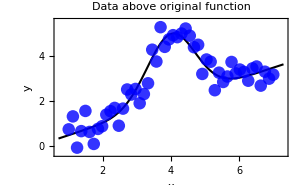

```mathematica
<<CIP`Graphics`

labels={"x","y","Data above original function"};
CIP`Graphics`PlotXyErrorDataAboveFunction[
	xyErrorData,
	pureOriginalFunction,
	labels]
```

The CurveFit package

```mathematica
<<CIP`CurveFit`
```

allows the generated data to be fitted with a structural model function with 3 unknown parameters a, b and c that corresponds to the original function used for the data generation:

```mathematica
modelFunction=a*x+b*Exp[-(x-c)^2];
argumentOfModelFunction=x;
parametersOfModelFunction={a,b,c};

curveFitInfoModel=CIP`CurveFit`FitModelFunction[
	xyErrorData,
	modelFunction,
	argumentOfModelFunction,
	parametersOfModelFunction];
```

The fit result is coded in a CurveFit info data structure (described in detail in the CurveFit package code) and may be inspected by the ShowFitResult method:

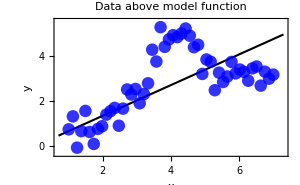

```mathematica
CIP`CurveFit`ShowFitResult[
	{"FunctionPlot"},
	xyErrorData,
	curveFitInfoModel]
```

By graphical inspection it becomes obvious that the fit attempt failed: The obtained model function does not adequately represent the erroneous data. What happened? Internally the FitModelFunction method performs a local minimization procedure of the statistical quantity χ^2(a,b,c)=∑_(i=1)^50 ((y_i-f(x_i))/σ_i)^2 (following the “Method of Least Squares”) that starts at randomly generated values for the parameters a, b and c: For this distinct non-linear minimization problem these random start values were simply unfavorable (but they may work perfectly for other fitting procedures) so that the optimization procedure was not able to reach the global minimum of χ^2(a,b,c). Note, that this failure can not be traced to a deficiency of the minimization algorithm (in fact Mathematica uses a very robust state-of-the-art algorithmic implementation) but is a principal problem of local minimization which does not necessarily converge to the global minimum in general (as the terminus “local” already implies). To improve the parameters’ start values an initial global search with adequate search intervals for each of the 3 parameters a, b and c of the model function

```mathematica
searchIntervalForA={0.,10.};
searchIntervalForB={0.,10.};
searchIntervalForC={0.,10.};
parameterSearchIntervals=
	{searchIntervalForA,
	searchIntervalForB,
	searchIntervalForC};
```

should be performed (CIP function GetStartParameters uses the Differential Evolution method as a default for the global search in the defined search space):

```mathematica
startParameters=CIP`CurveFit`GetStartParameters[
	xyErrorData,
	modelFunction,
	argumentOfModelFunction,
	parametersOfModelFunction,
	parameterSearchIntervals]
```

{{a,0.50081},{b,3.37605},{c,3.85658}}

With the obtained improved parameters’ start values and a desired confidence level of 99.9% for the parameters’ errors (instead of the default standard 68.3%)

```mathematica
confidenceLevelOfParameterErrors=0.999;

curveFitInfoModel=CIP`CurveFit`FitModelFunction[
	xyErrorData,
	modelFunction,
	argumentOfModelFunction,
	parametersOfModelFunction,
	CurveFitOptionStartParameters->startParameters,
	CurveFitOptionConfidenceLevel->
		confidenceLevelOfParameterErrors];
```

the internal minimization procedure now arrives at the global minimum with a convincing fit result:

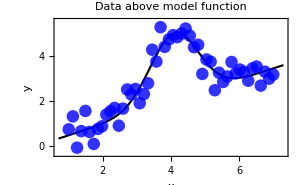

```mathematica
CIP`CurveFit`ShowFitResult[
	{"FunctionPlot"},
	xyErrorData,
	curveFitInfoModel]
```

The residuals plot with the deviations between fitted curve and data shows random and non-systematic residuals (y_i-f(x_i)),

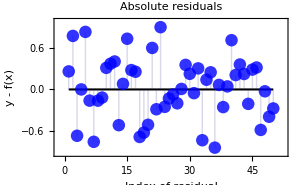

Standard deviation of fit = 4.519×10^-1

Out 1 : Correlation coefficient = 0.952215

```mathematica
CIP`CurveFit`ShowFitResult[
	{"AbsoluteResidualsPlot","SDFit",
		"CorrelationCoefficient"},
	xyErrorData,
	curveFitInfoModel]
```

a standard deviation of the fit of 0.4519 which is near the standard deviation (error) of 0.5 used for the data generation and a (Pearson) correlation coefficient near 1. The χ_red^2 value (“reduced chi-square”, which balances the residuals with the provided statistical errors σ_i of the y_i values and should be 1 on average since residuals and statistical errors should be comparable in size)

```mathematica
CIP`CurveFit`ShowFitResult[
	{"ReducedChiSquare","ParameterErrors"},
	xyErrorData,
	curveFitInfoModel]
```

Reduced chi-square of fit = 8.17×10^-1

| Value | Standard error | Confidence region
Parameter | a -> 0.495279 | 0.0205374 | {0.423195, 0.567363}
Parameter | b -> 3.01029 | 0.196361 | {2.32109, 3.6995}
Parameter | c -> 4.09318 | 0.0528048 | {3.90784, 4.27852}

of 0.817 is near 1 as expected for a good fit and the parameter values used for data generation (a = 0.5, b=3.0, c=4.0) are within the 99.9% confidence region of the estimated parameter values. The CurveFit info data structure may be used for model-based calculations, e.g. for the determination of the maximum value of the model function in the interval spanned by the data:

```mathematica
pureModelFunction=Function[argument,
	CIP`CurveFit`CalculateFunctionValue[
		argument,
		curveFitInfoModel]
	];

FindMaximum[pureModelFunction[argument],
	{argument,xMin,xMax}]
```

{5.058,{argument→4.17601}}

The result is near the true maximum of the original function:

```mathematica
FindMaximum[pureOriginalFunction[argument],
	{argument,xMin,xMax}]
```

{5.02091,{argument→4.08393}}

For practical purposes it is often interesting to estimate the necessary number of data with a specific statistical error in advance which are able to achieve a desired width of the confidence region of a specific parameter. In the above fit procedure 50 xy-error data triples with an absolute error (standard deviation) of 0.5 were able to achieve a 99.9% confidence region of parameter c with width (4.27852-3.90784)=0.37068. If the 99.9% confidence region of parameter c (with index 3 in definition parametersOfModelFunction above) should be reduced from 0.37068 to 0.1 (i.e. the parameter value estimation should be more reliable) the number of xy-error triples has to be increased to

```mathematica
indexOfParameter=3;
desiredWidthOfConfidenceRegion=0.1;

numberOfData=CIP`CurveFit`GetNumberOfData[
	desiredWidthOfConfidenceRegion,
	indexOfParameter,
	pureOriginalFunction,
	argumentRange,
	standardDeviationRange,
	modelFunction,
	argumentOfModelFunction,
	parametersOfModelFunction,
	CurveFitOptionStartParameters->startParameters,
	CurveFitOptionConfidenceLevel->
		confidenceLevelOfParameterErrors]
```

630

630 data triples, i.e. for a reduction of the confidence region of about factor 4 the number of data has to be increased more than twelve fold. Another practical issue affects the statistical errors σ_i of the y_i values: Often the true statistical errors are unknown and only weights are used. If all xy pairs from above

```mathematica
xyData=xyErrorData[[All,{1,2}]];
```

are attributed with the weight 1.0 (an operation which may be performed with the AddErrorToXYData method of the DataTransformation package)

```mathematica
<<CIP`DataTransformation`

weight=1.;
xyWeightData=CIP`DataTransformation`AddErrorToXYData[
	xyData,
	weight];
```

the weights may be “corrected to errors” by an appropriate factor to obtain a χ_red^2 value of 1 after the fit to yield “reasonable” parameter errors and confidence regions. This correction can be specified with the variance estimator option

```mathematica
varianceEstimator="ReducedChiSquare";

curveFitInfoCorrected=CIP`CurveFit`FitModelFunction[
	xyWeightData,
	modelFunction,
	argumentOfModelFunction,
	parametersOfModelFunction,
	CurveFitOptionStartParameters->startParameters,
	CurveFitOptionConfidenceLevel->
		confidenceLevelOfParameterErrors,
	CurveFitOptionVarianceEstimator->varianceEstimator];
```

and leads to parameter error and confidence region estimates comparable to the true values above

```mathematica
CIP`CurveFit`ShowFitResult[
	{"ReducedChiSquare","ParameterErrors"},
	xyWeightData,
	curveFitInfoCorrected]
```

Reduced chi-square of fit = 2.043×10^-1

| Value | Standard error | Confidence region
Parameter | a -> 0.495279 | 0.0185635 | {0.430123, 0.560435}
Parameter | b -> 3.01029 | 0.177488 | {2.38733, 3.63326}
Parameter | c -> 4.09318 | 0.0477297 | {3.92565, 4.2607}

although errors/weights of value 1.0 were arbitrary (and in this case too large which is indicated by the small χ_red^2 value of the fit of only 0.2043 which is clearly below 1).
If a structural model function is not known the xy-error triples may be represented by a smooth and balancing curve which has to be constructed by an appropriate data smoothing procedure. The CIP construction process creates smoothing cubic splines with a minimum overall curvature to arrive at a predefined χ_red^2 value which must be specified as an initial hyper-parameter: A value above 1.0 indicates that on average the residuals are allowed to be larger than the statistical errors σ_i of the y_i values and the smooth and balancing curve tends to become a straight line. A value below 1.0 leads to the opposite, i.e. to a curve that tends to touch every single xy data pair which results in a mere interpolation between the xy pairs. A χ_red^2 value around 1.0 is usually a good compromise if true statistical errors σ_i of the y_i values are available:

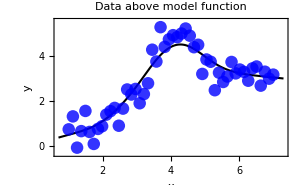

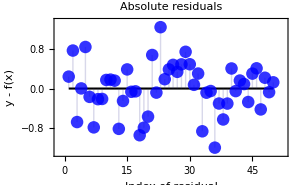

Reduced chi-square of fit = 1.

```mathematica
reducedChiSquare=1.;
curveFitInfoSmoothing=CIP`CurveFit`FitCubicSplines[
	xyErrorData,
	reducedChiSquare];
CIP`CurveFit`ShowFitResult[
	{"FunctionPlot","AbsoluteResidualsPlot",
		"ReducedChiSquare"},
	xyErrorData,
	curveFitInfoSmoothing];
```

The residuals plot shows a local systematic positive deviation near the maximum curved peak region of the data since the CIP smoothing method tends to minimize overall curvature for the given value of χ_red^2. The maximum of the smoothing curve is calculated to be at

```mathematica
pureSmoothingFunction=Function[argument,
	CIP`CurveFit`CalculateFunctionValue[
		argument,
		curveFitInfoSmoothing]
	];

FindMaximum[pureModelFunction[argument],
	{argument,xMin,xMax}]
```

{5.058,{argument→4.17601}}

Finally the model fit and smoothing results may be summarized in a single overlay

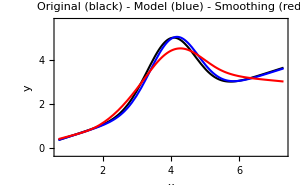

```mathematica
functionValueRange={0.,5.5};
plotStyle=
	{{Thickness[0.005], Black},
	{Thickness[0.005], Blue},
	{Thickness[0.005], Red}};
labels={"x","y",
	"Original (black) - Model (blue) - Smoothing (red)"};
CIP`Graphics`Plot2dFunctions[
	{pureOriginalFunction,pureModelFunction,
		pureSmoothingFunction},
	argumentRange,
	functionValueRange,
	plotStyle,
	labels]
```

to illustrate their quality. All three curves will tend to coincide if the number of xy-error triples is increased or the statistical errors σ_i of the y_i values are decreased (e.g. by an improved experimental setup).

### Clustering and Machine Learning

Machine learning methods are applied when K input/output (I/O) pairs

((x̲)_1,(y̲)_1),...,((x̲)_K,(y̲)_K)

of inputs

(x̲)_k=(x_(k 1),x_(k 2),...,x_(k M))   ;   k=1,...,K

and corresponding outputs

(y̲)_k=(y_(k 1),y_(k 2),...,y_(k N))   ;   k=1,...,K

are available but the model functions f_i that map the input vectors onto the output components

y_i=f_i(x_1,...,x_M)   ;   i=1,...,N

are completely unknown: Machine learning tries to approximate these unknown model functions f_i on the basis of the provided I/O data by an appropriate combination of method-dependent elementary functions. This situation is comparable to 2D data smoothing discussed above but now takes place in many more dimensions. Clustering tries to analyze the structure/distribution of the individual inputs (x̲)_k in the input space by partitioning them into an appropriate number of groups/clusters.

Data for machine learning are coded in a data set structure which is a list of input/output (I/O) pairs, e.g.

```mathematica
dataSet={ioPair1,ioPair2,ioPair3};
```

Each I/O pair consists of an input and an output

```mathematica
ioPair1={input1,output1};
ioPair2={input2,output2};
ioPair3={input3,output3};
```

where each input and each output is a vector/list with a defined number of components, e.g.

```mathematica
input1={Subscript[in, 11],Subscript[in, 12],Subscript[in, 13]};
output1={Subscript[out, 11],Subscript[out, 12]};

input2={Subscript[in, 21],Subscript[in, 22],Subscript[in, 23]};
output2={Subscript[out, 21],Subscript[out, 22]};

input3={Subscript[in, 31],Subscript[in, 32],Subscript[in, 33]};
output3={Subscript[out, 31],Subscript[out, 32]};
```

The whole example data set combines to:

```mathematica
dataSet
```

{{{in_11,in_12,in_13},{out_11,out_12}},{{in_21,in_22,in_23},{out_21,out_22}},{{in_31,in_32,in_33},{out_31,out_32}}}

With methods of the Utility package

```mathematica
<<CIP`Utility`
```

the inputs and outputs of a data set can be extracted:

```mathematica
inputs=CIP`Utility`GetInputsOfDataSet[dataSet]
```

{{in_11,in_12,in_13},{in_21,in_22,in_23},{in_31,in_32,in_33}}

```mathematica
outputs=CIP`Utility`GetOutputsOfDataSet[dataSet]
```

{{out_11,out_12},{out_21,out_22},{out_31,out_32}}

Inputs are the data structure for clustering tasks, e.g.

```mathematica
input1={Subscript[in, 11],Subscript[in, 12],Subscript[in, 13]};
input2={Subscript[in, 21],Subscript[in, 22],Subscript[in, 23]};
input3={Subscript[in, 31],Subscript[in, 32],Subscript[in, 33]};
inputs={input1,input2,input3}
```

{{in_11,in_12,in_13},{in_21,in_22,in_23},{in_31,in_32,in_33}}

and are performed with the Cluster package:

```mathematica
<<CIP`Cluster`
```

A clustering procedure tries to partition the individual inputs of the input space into separated regions (groups/clusters) according to specific criteria, e.g. if the following random 2D inputs

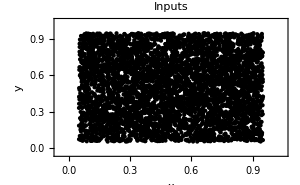

```mathematica
SeedRandom[1];
inputs=Table[
	{RandomReal[{0.05,0.95}],RandomReal[{0.05,0.95}]},
	{5000}
];

argumentRange={0.,1.};
functionValueRange={0.,1.};
labels={"x","y","Inputs"};
inputsWithPlotStyle={inputs,{PointSize[0.01],Black}};
points2DWithPlotStyleList={inputsWithPlotStyle};
CIP`Graphics`PlotMultiple2dPoints[
	points2DWithPlotStyleList,
	labels,
	GraphicsOptionArgumentRange2D->argumentRange,
	GraphicsOptionFunctionValueRange2D->functionValueRange]
```

are to be partitioned into 3 groups/clusters

```mathematica
numberOfClusters=3;
```

with the CIP default k-medoids clustering method

```mathematica
clusterInfo=CIP`Cluster`GetFixedNumberOfClusters[
	inputs,
	numberOfClusters];
```

(the clustering result is coded in a Cluster info data structure described in detail in the Cluster package code) a visual inspection of the resulting clusters shows

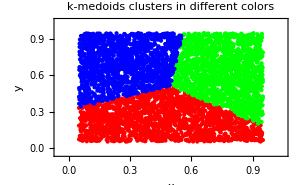

```mathematica
inputsOfClusterList=Table[
	CIP`Cluster`GetInputsOfCluster[
		inputs,
		indexOfCluster,
		clusterInfo],
	{indexOfCluster,numberOfClusters}
];
colorList={Red,Green,Blue};
points2DWithPlotStyleList=Table[
	{inputsOfClusterList[[i]],
		{PointSize[0.01],colorList[[i]]}},
	{i,numberOfClusters}
];
labels={"x","y","k-medoids clusters in different colors"};
CIP`Graphics`PlotMultiple2dPoints[
	points2DWithPlotStyleList,
	labels,
	GraphicsOptionArgumentRange2D->argumentRange,
	GraphicsOptionFunctionValueRange2D->functionValueRange]
```

that they are partitioned according to their euclidean distance. Alternative clustering methods like ART-2a

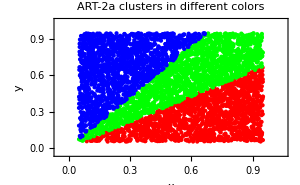

```mathematica
clusterMethod="ART2a";
clusterInfoART2a=CIP`Cluster`GetFixedNumberOfClusters[
	inputs,
	numberOfClusters,
	ClusterOptionMethod->clusterMethod];

inputsOfClusterList=Table[
	CIP`Cluster`GetInputsOfCluster[
		inputs,
		indexOfCluster,
		clusterInfoART2a],
	{indexOfCluster,numberOfClusters}
];
points2DWithPlotStyleList=Table[
	{inputsOfClusterList[[i]],
		{PointSize[0.01],colorList[[i]]}},
	{i,numberOfClusters}
];
labels={"x","y","ART-2a clusters in different colors"};
CIP`Graphics`PlotMultiple2dPoints[
	points2DWithPlotStyleList,
	labels,
	GraphicsOptionArgumentRange2D->argumentRange,
	GraphicsOptionFunctionValueRange2D->functionValueRange]
```

try to partition from a “radial point of view”. The quality of the constructed clusters may be evaluated by an appropriate measure like the so called silhouette width: For each single input a silhouette width value between -1 and 1 is calculated where a value near 1 means that the mean distance of the single input to the other inputs of its own cluster is far smaller than the mean distance to the inputs of its nearest cluster which indicates “good clustering”. A value near -1 means the opposite: A “poor clustering” because the single input should be assigned to its nearest cluster and not to the currently assigned cluster. A value around 0 means that the single input is on the border between its own and its nearest cluster. If the silhouette width is calculated for all inputs a mean silhouette width for a partitioning approach with a specified number of clusters may be obtained as a decision criterion for evaluating the optimum number of clusters: The higher the mean silhouette width of a clustering approach the better the clustering result. This may be illustrated by an intuitive example of inputs that form 4 different clusters in the input space:

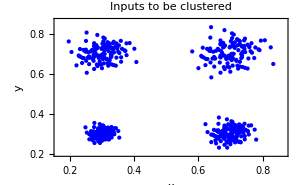

```mathematica
centroid1={0.3,0.3};
standardDeviation1=0.02;
numberOfCloudInputs1=150;
cloudDefinition1={centroid1,
	numberOfCloudInputs1,standardDeviation1};
inputs1=CIP`CalculatedData`GetDefinedGaussianCloud[
	cloudDefinition1];

centroid2={0.7,0.3};
standardDeviation2=0.03;
numberOfCloudInputs2=140;
cloudDefinition2={centroid2,
	numberOfCloudInputs2,standardDeviation2};
inputs2=CIP`CalculatedData`GetDefinedGaussianCloud[
	cloudDefinition2];

centroid3={0.3,0.7};
standardDeviation3=0.04;
numberOfCloudInputs3=130;
cloudDefinition3={centroid3,
	numberOfCloudInputs3,standardDeviation3};
inputs3=CIP`CalculatedData`GetDefinedGaussianCloud[
	cloudDefinition3];

centroid4={0.7,0.7};
standardDeviation4=0.05;
numberOfCloudInputs4=120;
cloudDefinition4={centroid4,
	numberOfCloudInputs4,standardDeviation4};
inputs4=CIP`CalculatedData`GetDefinedGaussianCloud[
	cloudDefinition4];

inputs=Join[inputs1,inputs2,inputs3,inputs4];

labels={"x","y","Inputs to be clustered"};
points2DWithPlotStyle={inputs,{PointSize[0.01],Blue}};
points2DWithPlotStyleList={points2DWithPlotStyle};
CIP`Graphics`PlotMultiple2dPoints[
	points2DWithPlotStyleList,
	labels]
```

The (default k-medoids) GetClusters method

```mathematica
clusterInfo=CIP`Cluster`GetClusters[inputs];
```

detects the optimum number of clusters to be 4 as expected:

```mathematica
CIP`Cluster`ShowClusterResult[
	{"NumberOfClusters"},
	clusterInfo]
```

Number of clusters = 4

The clustering result may be analyzed with respect to the euclidean distance of the detected cluster centroids

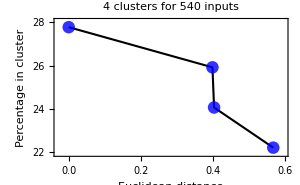

```mathematica
CIP`Cluster`ShowClusterResult[
	{"EuclideanDistanceDiagram"},
	clusterInfo]
```

or graphically illustrated (with the cluster centroids highlighted in black):

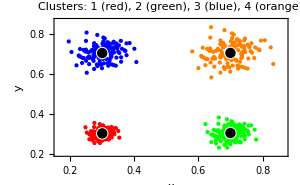

```mathematica
indexOfCluster=1;
inputsOfCluster1=CIP`Cluster`GetInputsOfCluster[
	inputs,
	indexOfCluster,
	clusterInfo];
indexOfCluster=2;
inputsOfCluster2=CIP`Cluster`GetInputsOfCluster[
	inputs,
	indexOfCluster,
	clusterInfo];
indexOfCluster=3;
inputsOfCluster3=CIP`Cluster`GetInputsOfCluster[
	inputs,
	indexOfCluster,
	clusterInfo];
indexOfCluster=4;
inputsOfCluster4=CIP`Cluster`GetInputsOfCluster[
	inputs,
	indexOfCluster,
	clusterInfo];

centroidVectors=CIP`Cluster`GetClusterProperty[
	{"CentroidVectors"},
	clusterInfo][[1]];
centroidVectorsBackground={centroidVectors,
	{PointSize[0.03],White}};
centroidVectorsWithPlotStyle={centroidVectors,
	{PointSize[0.025],Black}};

labels={"x","y",
	"Clusters: 1 (red), 2 (green), 3 (blue), 4 (orange)"};
points2DWithPlotStyle1={inputsOfCluster1,
	{PointSize[0.01],Red}};
points2DWithPlotStyle2={inputsOfCluster2,
	{PointSize[0.01],Green}};
points2DWithPlotStyle3={inputsOfCluster3,
	{PointSize[0.01],Blue}};
points2DWithPlotStyle4={inputsOfCluster4,
	{PointSize[0.01],Orange}};
points2DWithPlotStyleList={
	points2DWithPlotStyle1,
	points2DWithPlotStyle2,
	points2DWithPlotStyle3,
	points2DWithPlotStyle4,
	centroidVectorsBackground,
	centroidVectorsWithPlotStyle};
CIP`Graphics`PlotMultiple2dPoints[
	points2DWithPlotStyleList,
	labels]
```

The mean silhouette widths for partitioning with different numbers of clusters

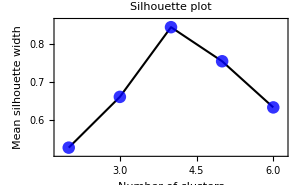

```mathematica
minimumNumberOfClusters=2;
maximumNumberOfClusters=6;
silhouettePlotPoints=CIP`Cluster`GetSilhouettePlotPoints[
	inputs,
	minimumNumberOfClusters,
	maximumNumberOfClusters];
CIP`Cluster`ShowSilhouettePlot[silhouettePlotPoints]
```

show a maximum value for 4 clusters which was consequently chosen by the GetClusters method. If the individual silhouette widths of the single inputs of the clusters are inspected

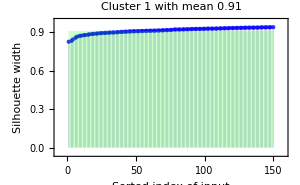

```mathematica
silhouetteStatisticsForClusters=
	CIP`Cluster`GetSilhouetteStatisticsForClusters[
		inputs,
		clusterInfo];

indexOfCluster=1;
CIP`Cluster`ShowSilhouetteWidthsForCluster[
	silhouetteStatisticsForClusters,
	indexOfCluster]
```

they are all found to be near 1 (which means “good clustering”)

```mathematica
Do[
	Print["Mean silhouette width of cluster ",
		indexOfCluster,
		" = ",
		silhouetteStatisticsForClusters[[indexOfCluster,
			1,2]]],
	{indexOfCluster,1,4}
]
```

Mean silhouette width of cluster 1 = 0.91

Mean silhouette width of cluster 2 = 0.86

Mean silhouette width of cluster 3 = 0.82

Mean silhouette width of cluster 4 = 0.77

but the cluster quality drops from cluster 1 to 4 since the mean silhouette widths of the individual clusters drop from 0.91 of cluster 1 to 0.77 of cluster 4. This corresponds to the obvious spread of the single inputs in the 4 clusters which increases from cluster 1 to cluster 4.

An important application of clustering with an a priori fixed number of clusters is the generation of a reduced number of representatives of a full set of inputs with a similar spatial diversity as the full set: This means that the few representatives should cover a similar input space as the full set of inputs. As an example the following input space with  470+470+10+10+10=970 single inputs

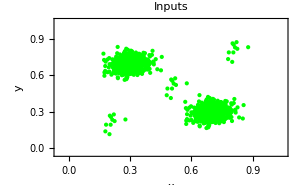

```mathematica
centroid1={0.3,0.7};
standardDeviation1=0.05;
numberOfCloudInputs1=470;
cloudDefinition1={centroid1,
	numberOfCloudInputs1,standardDeviation1};
inputs1=CIP`CalculatedData`GetDefinedGaussianCloud[
	cloudDefinition1];

centroid2={0.7,0.3};
standardDeviation2=0.05;
numberOfCloudInputs2=470;
cloudDefinition2={centroid2,
	numberOfCloudInputs2,standardDeviation2};
inputs2=CIP`CalculatedData`GetDefinedGaussianCloud[
	cloudDefinition2];

centroid3={0.5,0.5};
standardDeviation3=0.05; 
numberOfCloudInputs3=10;
cloudDefinition3={centroid3,
	numberOfCloudInputs3,standardDeviation3};
inputs3=CIP`CalculatedData`GetDefinedGaussianCloud[
	cloudDefinition3];

centroid4={0.8,0.8};
standardDeviation4=0.05; 
numberOfCloudInputs4=10;
cloudDefinition4={centroid4,
	numberOfCloudInputs4,standardDeviation4};
inputs4=CIP`CalculatedData`GetDefinedGaussianCloud[
	cloudDefinition4];

centroid5={0.2,0.2};
standardDeviation5=0.05; 
numberOfCloudInputs5=10;
cloudDefinition5={centroid5,
	numberOfCloudInputs5,standardDeviation5};
inputs5=CIP`CalculatedData`GetDefinedGaussianCloud[
	cloudDefinition5];

inputs=Join[inputs1,inputs2,inputs3,inputs4,inputs5];
labels={"x","y","Inputs"};
inputsWithPlotStyle={inputs,{PointSize[0.01],Green}};
points2DWithPlotStyleList={inputsWithPlotStyle};
CIP`Graphics`PlotMultiple2dPoints[
	points2DWithPlotStyleList,
	labels,
	GraphicsOptionArgumentRange2D->argumentRange,
	GraphicsOptionFunctionValueRange2D->functionValueRange]
```

is to be represented by 20 representative inputs (representatives).

```mathematica
numberOfRepresentatives=20;
```

The first choice might be a random selection of the representatives

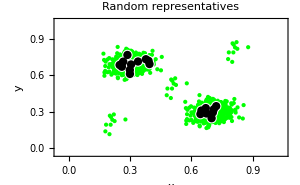

```mathematica
numberOfRepresentatives=20;
randomRepresentatives=
	CIP`Cluster`GetRandomRepresentatives[
		inputs,
		numberOfRepresentatives];
labels={"x","y","Random representatives"};
randomRepresentativesBackground={randomRepresentatives,
	{PointSize[0.025],White}};
randomRepresentativesWithPlotStyle={randomRepresentatives,
	{PointSize[0.02],Black}};
points2DWithPlotStyleList=
	{inputsWithPlotStyle,randomRepresentativesBackground,
		randomRepresentativesWithPlotStyle};
CIP`Graphics`PlotMultiple2dPoints[
	points2DWithPlotStyleList,
	labels,
	GraphicsOptionArgumentRange2D->argumentRange,
	GraphicsOptionFunctionValueRange2D->functionValueRange]
```

but this often leads to the visible over-representation of input space regions with a high density of inputs: The selected representatives do not possess the spatial diversity of the full set of inputs. If representatives are generated by an adequate clustering process with the number of a priori fixed clusters to be the number of desired representatives and the representatives are chosen to be those inputs which are nearest to the detected cluster centroids

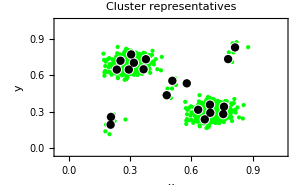

```mathematica
clusterRepresentatives=
	CIP`Cluster`GetClusterRepresentatives[
		inputs,
		numberOfRepresentatives];
labels={"x","y","Cluster representatives"};
clusterRepresentativesBackground={clusterRepresentatives,
	{PointSize[0.025],White}};
clusterRepresentativesWithPlotStyle={clusterRepresentatives,
	{PointSize[0.02],Black}};
points2DWithPlotStyleList=
	{inputsWithPlotStyle,clusterRepresentativesBackground,
	clusterRepresentativesWithPlotStyle};
CIP`Graphics`PlotMultiple2dPoints[
	points2DWithPlotStyleList,
	labels,
	GraphicsOptionArgumentRange2D->argumentRange,
	GraphicsOptionFunctionValueRange2D->functionValueRange]
```

the situation improves considerably as demonstrated. The distribution of representatives now covers a more similar region of input space compared to the full set of inputs.

Cluster analysis may also provide insights for classification tasks tackled by machine learning where the machine is trained to assign an input to a specific known class. Within CIP a classification data set is coded with outputs that contain a component for every class with a component value of 1.0 for the specific assigned class and 0.0 for all others. As an example the coding of 3 classes leads to the following outputs for

class 1: (1.0
0.0
0.0) , class 2: (0.0
1.0
0.0)  and class 3: (0.0
0.0
1.0)

To assign an input to a specific class after learning the maximum component of the machine-calculated output is determined: The attributed class then corresponds to the position of this maximum component, e.g. if a trained machine learning method calculates the output

(0.2
0.5
0.3)

for a specific input then this input is assigned to class 2 since component 2 (0.5) is the maximum component of the calculated output. As an (inevitable) example the (famous) iris flower classification is chosen (the data are available from the ExperimentalData package):

```mathematica
<<CIP`ExperimentalData`

irisFlowerDataSet=
	CIP`ExperimentalData`GetIrisFlowerClassificationDataSet[];
```

The iris flower data set contains

```mathematica
CIP`Graphics`ShowDataSetInfo[
	{"IoPairs","InputComponents","OutputComponents",
		"ClassCount"},
	irisFlowerDataSet]
```

Number of IO pairs = 150

Number of input components = 4

Number of output components = 3

Class 1 with 50 members

Class 2 with 50 members

Class 3 with 50 members

150 I/O pairs with inputs that contain 4 components that represent 4 quantitative features of iris flowers. These 150 inputs are assigned to 3 classes that represent the corresponding iris flower species (thus an output contains 3 components to code 3 classes as described above) where each class is represented by 50 I/O pairs. The classification data set can be sorted according to their classes

```mathematica
sortResult=
	CIP`DataTransformation`SortClassificationDataSet[
		irisFlowerDataSet];
sortedIrisFlowerDataSet=sortResult[[1]];
classIndexMinMaxList=sortResult[[2]]
```

{{1,50},{51,100},{101,150}}

where the indices of class specific I/O pairs may be obtained by a classIndexMinMaxList (which means that I/O pairs 1 to 50 of sortedIrisFlowerDataSet belong to class 1, I/O pairs 51 to 100 belong to class 2 and I/O pairs 101 to 150 belong to class 3). The pure inputs of the sorted iris flower classification data set may be obtained

```mathematica
sortedIrisFlowerInputs=
	CIP`Utility`GetInputsOfDataSet[
		sortedIrisFlowerDataSet];
```

for a cluster analysis:

```mathematica
clusterInfo=CIP`Cluster`GetClusters[
	sortedIrisFlowerInputs];
CIP`Cluster`ShowClusterResult[
	{"NumberOfClusters"},
	clusterInfo]
```

Number of clusters = 2

The default k-medoids clustering method detects 2 cluster which may be confirmed by plot of the means silhouette widths

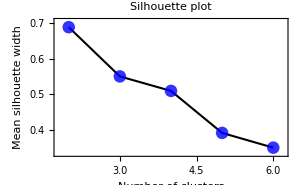

```mathematica
minimumNumberOfClusters=2;
maximumNumberOfClusters=6;
silhouettePlotPoints=CIP`Cluster`GetSilhouettePlotPoints[
	sortedIrisFlowerInputs,
	minimumNumberOfClusters,
	maximumNumberOfClusters];
CIP`Cluster`ShowSilhouettePlot[silhouettePlotPoints]
```

where 2 clusters achieve the maximum value. The quality of the clusters may be evaluated by inspection of the individual silhouette widths: Cluster 1

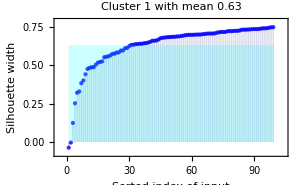

```mathematica
silhouetteStatisticsForClusters=
	CIP`Cluster`GetSilhouetteStatisticsForClusters[
		sortedIrisFlowerInputs,
		clusterInfo];
indexOfCluster=1;
CIP`Cluster`ShowSilhouetteWidthsForCluster[
	silhouetteStatisticsForClusters,
	indexOfCluster]
```

is a “poor cluster”, i.e. this cluster embraces a non-well separated region of inputs indicated by single silhouette widths around 0. The second cluster 2

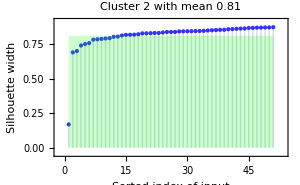

```mathematica
indexOfCluster=2;
CIP`Cluster`ShowSilhouetteWidthsForCluster[
	silhouetteStatisticsForClusters,
	indexOfCluster]
```

is a comparatively “good cluster” that comprises inputs that are clearly separated in the input space. Since the class assignments of all single inputs are known this information may be used to visualize the percentage of class members that occupy a detected cluster:

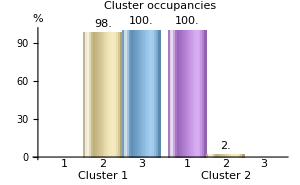

```mathematica
clusterOccupancies=CIP`Cluster`GetClusterOccupancies[
	classIndexMinMaxList,
	clusterInfo];
CIP`Cluster`ShowClusterOccupancies[clusterOccupancies]
```

It becomes obvious that cluster 2 contains all (100%) inputs of class 1 and only 2% of inputs of class 2 thus class 1 related inputs are confined to a nearly separated region of the input space. Class 2 and 3 related inputs are nearly completely united in cluster 1 so their spatial distance in the input space does not lead to a clear separation. If the clustering process is forced to cluster the iris flower inputs into 3 clusters

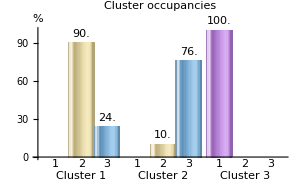

```mathematica
numberOfClusters=3;
clusterInfo=CIP`Cluster`GetFixedNumberOfClusters[
	sortedIrisFlowerInputs,
	numberOfClusters];

clusterOccupancies=CIP`Cluster`GetClusterOccupancies[
	classIndexMinMaxList,clusterInfo];
CIP`Cluster`ShowClusterOccupancies[clusterOccupancies]
```

all inputs of class 1 now are confined to cluster 3 (they are separated in input space which corresponds to the finding before) and the inputs of class 2 and 3 are mainly separated in the clusters 1 and 2 but with a distinct overlap (i.e. class 2 inputs are found in cluster 2 and class 3 inputs in cluster 1 respectively). This finding can be used to construct an unsupervised class predictor that assigns a specific class to an arbitrary single input if (i) the single input’s euclidean distances to the detected cluster’s centroids is calculated, (ii) the nearest cluster centroid is evaluated and (iii) this specific class is assigned to the single input whose inputs are dominant in the centroid’s cluster. If for the current example the centroid of cluster 1 would be the nearest to the single input this input would be assigned to class 2 since class 2 inputs dominate cluster 1. The term “unsupervised” in this context means that the class information was not used to construct the clusters. An unsupervised clustering-based class predictor is constructed with the FitCluster method:

```mathematica
clusterInfo=CIP`Cluster`FitCluster[irisFlowerDataSet];
```

For the iris flower data this unsupervised approach achieves an overall correct classification of the whole data set of nearly 90%:

```mathematica
CIP`Cluster`ShowClusterSingleClassification[
	{"CorrectClassification"},
	irisFlowerDataSet,
	clusterInfo]
```

89.3% correct classifications

If the success rates are evaluated per class

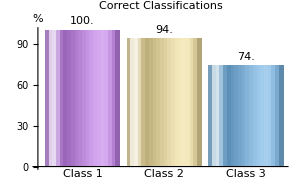

```mathematica
CIP`Cluster`ShowClusterSingleClassification[
	{"CorrectClassificationPerClass"},
	irisFlowerDataSet,
	clusterInfo]
```

it is found that class 1 predictions are “always right” but class 2 and 3 predictions may be increasingly erroneous. This is confirmed by the inverse view of the distribution of wrong classification predictions

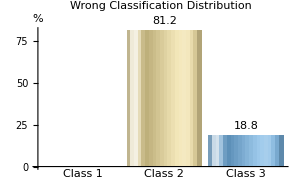

```mathematica
CIP`Cluster`ShowClusterSingleClassification[
	{"WrongClassificationDistribution"},
	irisFlowerDataSet,
	clusterInfo]
```

where class 2 predictions are most suspicious to be wrong. If ART-2a is used as an alternative clustering method for the construction of an unsupervised class predictor

```mathematica
clusterMethod="ART2a";
clusterInfo=CIP`Cluster`FitCluster[
	irisFlowerDataSet,
	ClusterOptionMethod->clusterMethod];
```

its overall performance of 87.3% correct predictions is similar to the k-medoids result with 89.3% but with differences in detail:

87.3% correct classifications

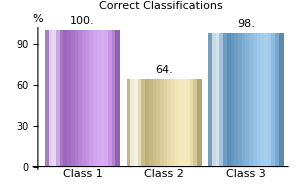

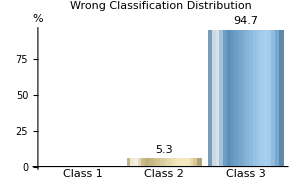

```mathematica
CIP`Cluster`ShowClusterSingleClassification[
	{"CorrectClassification",
		"CorrectClassificationPerClass",
		"WrongClassificationDistribution"},
	irisFlowerDataSet,
	clusterInfo]
```

With the construction of class predictors the realm of machine learning is entered: Unsupervised learning like the cluster-based class prediction above is extended to supervised learning where the outputs are explicitly utilized for the learning process. For a classification task a supervised learning method tries to construct an adequate decision surface on the basis of the outputs’ class assignment information above the input space. Multiple linear regression (MLR) may be used for machine learning but is confined to the construction of linear surfaces only.

```mathematica
<<CIP`MLR`
```

If applied to the iris flower classification task

```mathematica
mlrInfo=CIP`MLR`FitMlr[irisFlowerDataSet];
CIP`MLR`ShowMlrSingleClassification[
	{"CorrectClassification"},
	irisFlowerDataSet,
	mlrInfo]
```

84.7% correct classifications

the predictive success with only 84.7% of this supervised learning method is inferior to the unsupervised cluster-based learning attempts above, i.e. a linear method is not advised in this case (and is rather limited in general). Non-linear supervised learning is introduced with Multiple Polynomial Regression (MPR)

```mathematica
<<CIP`MPR`
```

where the polynomial order specifies the degree of allowed non-linearity (where a polynomial order of 1 means MLR). If a polynomial order of 2 is chosen

```mathematica
polynomialOrder=2;
```

the predictive success is considerably improved to 98% correct classifications:

98.% correct classifications

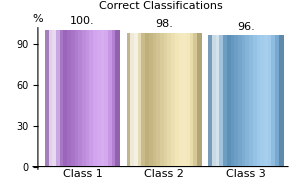

```mathematica
mprInfo=CIP`MPR`FitMpr[irisFlowerDataSet,polynomialOrder];
CIP`MPR`ShowMprSingleClassification[
	{"CorrectClassification",
		"CorrectClassificationPerClass"},
	irisFlowerDataSet,
	mprInfo]
```

But unlike unsupervised learning or linear supervised learning with MLR the application of non-linear supervised learning methods may lead to an unwanted phenomenon called overfitting: The method learns the I/O data in a “too perfect manner”, i.e. it creates a mere “I/O look-up table” rather than a true predictor: When asked to predict adequate outputs for unknown new inputs (not used for training) it fails utterly. Overfitting is a severe problem for machine learning and is usually tackled by partitioning a data set into a training set (used for supervised learning) and a test set (used for validation of the predictability after learning) where the inputs of training and test set should have a similar spatial distribution in the input space (so that predictability can be validated for all input space regions) and should be at least equal in size (where it holds: The smaller the training and the larger the test the more convincing the predictor). If the iris flower data are arbitrarily partitioned into a training set that contains 40% of the I/O pairs of the full data set and a corresponding test set with 60 of the I/O pairs (i.e. a training fraction of 0.4)

```mathematica
trainingFraction=0.4;
```

the training/test partitioning process may be performed with cluster representatives as described above to obtain a good spatial coverage of the whole input space for the training data. In addition the representative I/O pair in the training set of each cluster may be optimized heuristically with a number of trials

```mathematica
numberOfTrainingSetOptimizationSteps=10;
```

in combination with blacklisting (which avoids oscillations of I/O pair exchange for a specified number of steps)

```mathematica
blackListLength=5;
```

where the restriction of intra-cluster I/O pair exchange preservers the spatial diversity of the training set (which might get lost by an alternative inter-cluster exchange):

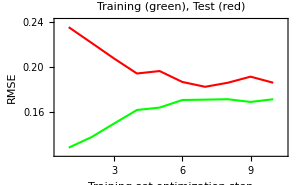

```mathematica
mprTrainOptimization=CIP`MPR`GetMprTrainOptimization[
	irisFlowerDataSet,
	polynomialOrder,
	trainingFraction,
	numberOfTrainingSetOptimizationSteps,
	UtilityOptionBlackListLength->blackListLength];
CIP`MPR`ShowMprTrainOptimization[mprTrainOptimization]
```

The inter-cluster exchange procedure leads to an improved predictability as indicated by a decreased root mean square error (RMSE) which measures the deviation between calculated machine learning outputs and the data outputs. The most predictive training/test combination is chosen

```mathematica
bestIndex=CIP`MPR`GetBestMprClassOptimization[
	mprTrainOptimization]
```

4

```mathematica
trainingAndTestSet=mprTrainOptimization[[3,bestIndex]];
trainingSet=trainingAndTestSet[[1]];
testSet=trainingAndTestSet[[2]];
mprInfo=mprTrainOptimization[[4,bestIndex]];
```

and can be analyzed: The supervised learning of the (smaller) training set achieves a rate of 98.3 % correct predictions (with an absolute number of 1 wrong classified I/O pair)

```mathematica
CIP`MPR`ShowMprSingleClassification[
	{"CorrectClassification","WrongClassificationPairs"},
	trainingSet,
	mprInfo]
```

98.3% correct classifications

Wrong I/O pair index = 60; input = {63., 28., 51., 15.}; class desired/machine = 3 / 2

and the validation with the (larger) test set arrives at a comparable success rate of 97.8% (with 2 wrong classified I/O pairs)

```mathematica
CIP`MPR`ShowMprSingleClassification[
	{"CorrectClassification","WrongClassificationPairs"},
	testSet,
	mprInfo]
```

97.8% correct classifications

Wrong I/O pair index = 1; input = {60., 27., 51., 16.}; class desired/machine = 2 / 3

Wrong I/O pair index = 11; input = {60., 22., 50., 15.}; class desired/machine = 3 / 2

Note that the non-linear MPR-order-2 class predictor is truly predictive (training and test set do have a similar spatial diversity in the input space, the test set size even exceeds the training set size and predictability on both sets is equally good) and is superior to the unsupervised cluster-based as well as the supervised linear predictors. If the polynomial order is increased to e.g. 5

```mathematica
polynomialOrder=5;
```

the learning of the full iris flower data set becomes “perfect” (100% correct class predictions):

```mathematica
mprInfo=CIP`MPR`FitMpr[irisFlowerDataSet,polynomialOrder];
CIP`MPR`ShowMprSingleClassification[
	{"CorrectClassification"},
	irisFlowerDataSet,
	mprInfo]
```

100.% correct classifications

But this apparent success is suspicious: If the full data set is again split into a (smaller 40%) training and a (larger 60%) test set (with optimized cluster representatives in the training set)

```mathematica
mprTrainOptimization=CIP`MPR`GetMprTrainOptimization[
	irisFlowerDataSet,
	polynomialOrder,
	trainingFraction,
	numberOfTrainingSetOptimizationSteps,
	UtilityOptionBlackListLength->blackListLength];

bestIndex=CIP`MPR`GetBestMprClassOptimization[
	mprTrainOptimization];

trainingAndTestSet=mprTrainOptimization[[3,bestIndex]];
trainingSet=trainingAndTestSet[[1]];
testSet=trainingAndTestSet[[2]];
mprInfo=mprTrainOptimization[[4,bestIndex]];
```

the learning success of the training data remains a perfect 100%

```mathematica
CIP`MPR`ShowMprSingleClassification[
	{"CorrectClassification"},
	trainingSet,
	mprInfo]
```

100.% correct classifications

but the predictability for the test data with 83.3% correct classifications is only poor:

```mathematica
CIP`MPR`ShowMprSingleClassification[
	{"CorrectClassification"},
	testSet,
	mprInfo]
```

83.3% correct classifications

This is a clear hint for overfitting: For the iris flower data a polynomial decision surface of order 5 becomes “too flexible” so it starts to simply “remember” the training data which leads to a significantly decreased predictability for unknown (test) data. Unfortunately the best or most appropriate polynomial order for a MPR learning approach is not known in advance: The optimization of this hyper-parameter has to be performed on top of the learning process - either by mere (educated) trial and error or by systematic investigation (like the increasing-polynomial-order approach above). As an alternative non-linear supervised learning method a three-layer feed-forward neural network (perceptron)

```mathematica
<<CIP`Perceptron`
```

may be used to construct an iris flower class predictor: The crucial hyper-parameter of perceptrons is the number of hidden neurons which determines its complexity and therefore its principal learning abilities (where inadequate over-the-top complexity again may lead to overfitting). With the minimum number of 1 hidden neuron

```mathematica
numberOfHiddenNeurons=1;
```

a predictive success rate of 99.3% on the full iris flower data set is already achieved:

```mathematica
perceptronInfo=CIP`Perceptron`FitPerceptron[
	irisFlowerDataSet,numberOfHiddenNeurons];
CIP`Perceptron`ShowPerceptronSingleClassification[
	{"CorrectClassification"},
	irisFlowerDataSet,
	perceptronInfo]
```

99.3% correct classifications

A further increase of the number of hidden neurons is not advised but a training/test set partitioning for validation is mandatory:

```mathematica
perceptronTrainOptimization=
	CIP`Perceptron`GetPerceptronTrainOptimization[
		irisFlowerDataSet,
		numberOfHiddenNeurons,
		trainingFraction,
		numberOfTrainingSetOptimizationSteps,
		UtilityOptionBlackListLength->blackListLength];

bestIndex=
	CIP`Perceptron`GetBestPerceptronClassOptimization[
		perceptronTrainOptimization];

trainingAndTestSet=
	perceptronTrainOptimization[[3,bestIndex]];
trainingSet=trainingAndTestSet[[1]];
testSet=trainingAndTestSet[[2]];
perceptronInfo=perceptronTrainOptimization[[4,bestIndex]];
```

The predictability for the training

```mathematica
CIP`Perceptron`ShowPerceptronSingleClassification[
	{"CorrectClassification"},
	trainingSet,
	perceptronInfo]
```

100.% correct classifications

and the test data

```mathematica
CIP`Perceptron`ShowPerceptronSingleClassification[
	{"CorrectClassification","WrongClassificationPairs"},
	testSet,
	perceptronInfo]
```

98.9% correct classifications

Wrong I/O pair index = 89; input = {63., 28., 51., 15.}; class desired/machine = 3 / 2

is equally convincing thus the constructed perceptron can be regarded as another excellent class predictor for iris flowers.

Unlike a classification task (where an output is modelled to result in a class assignment by a winner-take-all principle among the output components) a regression task requires the quantitative modelling of the values of each output component. As a regression example an experimental data set is used that describes the dependence of a kinetics quantity on the composition of an adhesive polymer mixture:

```mathematica
dataSet=CIP`ExperimentalData`GetAdhesiveKineticsDataSet[];
CIP`Graphics`ShowDataSetInfo[
	{"IoPairs","InputComponents","OutputComponents"},
	dataSet]
```

Number of IO pairs = 73

Number of input components = 3

Number of output components = 1

Each I/O pair is four-dimensional (inputs with three components, outputs with one component) so the complete data set can not be displayed with 2D or 3D graphics. But due to the experimental measurement setup it is possible to obtain subsets of data that are suitable for visual inspection in 3D by definition of an adequate polymer mass ratio which is the first input component. The experimental errors of the data are reported to be “in the order of 10% to 20% with some outliers” which is an essential information for the assessment of the goodness of regression and a corresponding hyper-parameter selection of the machine learning method in the following. A fast MLR regression analysis

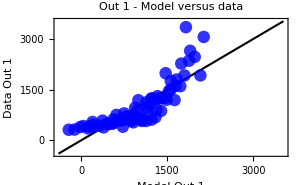

```mathematica
mlrInfo=CIP`MLR`FitMlr[dataSet];
CIP`MLR`ShowMlrSingleRegression[
	{"ModelVsDataPlot"},
	dataSet,
	mlrInfo];
```

yields a non-convincing model-versus-data plot: Systematic deviations are obvious and the residuals statistics show

```mathematica
CIP`MLR`ShowMlrSingleRegression[
	{"RelativeResidualsStatistics",
		"CorrelationCoefficient"},
	dataSet,
	mlrInfo];
```

Out 1 : Relative residuals (100*(Data - Model)/Data): Mean/Median/Maximum Value in % = 3.44×10^1 / 2.02×10^1 / 1.71×10^2

Out 1 : Correlation coefficient = 0.840707

that the magnitude of the mean deviation between data and model (over 30%) is obviously above the reported experimental errors of 10 to 20%. In addition the correlation coefficient is poor. So it can be deduced that the adhesive kinetics data can not be satisfactorily modelled by a linear technique. This may also be illustrated by the 3D display of a subset of the data that corresponds to a specific adequate polymer mass ratio of the mixture:

```mathematica
polymerMassRatio="80";
dataSet3D=
	CIP`ExperimentalData`GetAdhesiveKinetics3dDataSet[
		polymerMassRatio];

indexOfInput1=2;
indexOfInput2=3;
indexOfOutput=1;
input={80.,0.,0.};
pureMlr3dFunction=Function[{x,y},
	CIP`MLR`CalculateMlr3dValue[
		x,y,
		indexOfInput1,indexOfInput2,indexOfOutput,
		input,
		mlrInfo]
	];
labels={"In 2","In 3","Out 1"};
CIP`Graphics`Plot3dDataSetWithFunction[
	dataSet3D,
	pureMlr3dFunction,
	labels]
```

-Graphics3D-

The subset of data reveals a non-linear relationship between the composition of the polymer mixture and its corresponding kinetics quantity. Thus a non-linear machine learning method is indicated. If support vector machines (SVM) are chosen as a non-linear machine learning type

```mathematica
<<CIP`SVM`
```

an adequate kernel function (a crucial hyper-parameter of SVMs) is in need which is a priori not known. So a list of specific kernel functions is set up (in this case a Wavelet kernel with different widths as the kernel parameter is used)

```mathematica
kernelFunctionList=Table[
	{"Wavelet",kernelParameter},
	{kernelParameter,0.1,1.9,0.2}
];
```

and applied to the regression task:

```mathematica
svmInfoList=CIP`SVM`FitSvmSeries[
	dataSet,
	kernelFunctionList];
```

The result is a list with SVM info data structures that may be analyzed for their specific fitting success: Since the experimental errors are known the residuals obtained by an adequate SVM should be of comparable size. A plot of the mean deviations between the SVM predictions and the experimental data for the list of applied kernel functions

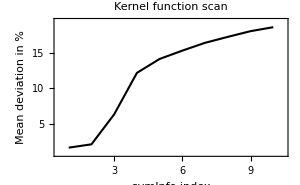

```mathematica
points2D={};
Do[
	svmInfo=svmInfoList[[index]];
	relativeResidualsStatistics=
		CIP`SVM`GetSvmRegressionResult[
			"RelativeResidualsStatistics",
			dataSet,
			svmInfo];
	outputIndex=1;
	meanDeviation=
		relativeResidualsStatistics[[outputIndex,1]];
	AppendTo[points2D,{index,meanDeviation}],
	{index,1,Length[svmInfoList]}
]

labels = {"svmInfo index", 
	"Mean deviation in %", "Kernel function scan"};
points2DWithPlotStyle = {points2D,
	{Thickness[0.005], Black}};
points2DWithPlotStyleList = {points2DWithPlotStyle};
CIP`Graphics`PlotMultiple2dLines[
	points2DWithPlotStyleList,
	labels
]
```

shows that a larger width of the wavelet kernel leads to larger mean deviations between model and data. But a mean deviation significantly smaller than the experimental errors like the one that is obtained with the first kernel function of the list (index 1: Wavelet kernel with a width of 0.1)

```mathematica
index=1;
kernelFunctionList[[index]]
```

{Wavelet,0.1}

indicates overfitting: The model is a mere data representation

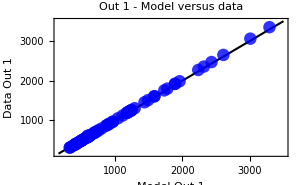

Out 1 : Relative residuals (100*(Data - Model)/Data): Mean/Median/Maximum Value in % = 1.67 / 1.43 / 4.74

Out 1 : Correlation coefficient = 0.999977

```mathematica
svmInfo=svmInfoList[[index]];
CIP`SVM`ShowSvmSingleRegression[
	{"ModelVsDataPlot","RelativeResidualsStatistics",
		"CorrelationCoefficient"},
	dataSet,
	svmInfo];
```

where the elementary kernel functions that build the full model surface just fit each single data point (visualized again with the subset of the adhesive kinetics data already used above):

```mathematica
pureSvm3dFunction=Function[{x,y},
	CIP`SVM`CalculateSvm3dValue[
		x,y,
		indexOfInput1,indexOfInput2,indexOfOutput,
		input,
		svmInfo]
	];
labels={"In 2","In 3","Out 1"};
CIP`Graphics`Plot3dDataSetWithFunction[
	dataSet3D,
	pureSvm3dFunction,
	labels]
```

-Graphics3D-

An adequate kernel that leads to residuals which are in concordance with the experimental errors like a Wavelet kernel with a width of 0.9 (index 5)

```mathematica
index=5;
kernelFunctionList[[index]]
```

{Wavelet,0.9}

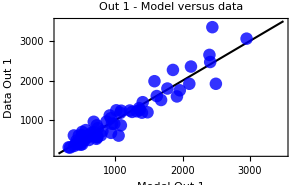

Out 1 : Relative residuals (100*(Data - Model)/Data): Mean/Median/Maximum Value in % = 1.41×10^1 / 1.1×10^1 / 7.19×10^1

Out 1 : Correlation coefficient = 0.954676

```mathematica
svmInfo=svmInfoList[[index]];
CIP`SVM`ShowSvmSingleRegression[
	{"ModelVsDataPlot","RelativeResidualsStatistics",
		"CorrelationCoefficient"},
	dataSet,
	svmInfo];
```

leads to a convincing (smooth and balancing) model function which is helpful for the adhesive scientist to calculate the kinetics quantity in the experimentally explored range of mixture compositions (note, that machine learning can not be used for extrapolations outside the experimental range in principle):

```mathematica
pureSvm3dFunction=Function[{x,y},
	CIP`SVM`CalculateSvm3dValue[
		x,y,
		indexOfInput1,indexOfInput2,indexOfOutput,
		input,
		svmInfo]
	];
CIP`Graphics`Plot3dDataSetWithFunction[
	dataSet3D,
	pureSvm3dFunction,
	labels]
```

-Graphics3D-

As a last example a minimal predictive classification model for the Wisconsin Diagnostic Breast Cancer (WDBC) data is constructed:

```mathematica
classificationDataSet=
	CIP`ExperimentalData`GetWDBCClassificationDataSet[];
CIP`Graphics`ShowDataSetInfo[
	{"IoPairs","InputComponents",
		"OutputComponents","ClassCount"},
	classificationDataSet]
```

Number of IO pairs = 569

Number of input components = 30

Number of output components = 2

Class 1 with 357 members

Class 2 with 212 members

The WDBC data set consists of 569 I/O pairs that correlate 30 features of cell nuclei extracted from breast tumor tissue (as input) with the tumor type after diagnosis (as output), i.e. they map the cell nuclei features onto a diagnosed benign (class 1) or malignant (class 2) tumor type. Thus the WDBC data may be used to construct a class predictor that supports the crucial benign/malignant decision in tumor diagnosis. As a non-linear machine learning method a perceptron with 3 hidden neurons (as the crucial hyper-parameter) is chosen:

```mathematica
numberOfHiddenNeurons=3;
```

To construct a minimal predictive model for a mapping of input features to the tumor type the smallest subset of input components/features that are necessary for a successful mapping is in need. To determine the most important input components a heuristic step-by-step procedure may be performed: In a first step all single input components are scanned for the one that leads to the best mapping from input to output with the highest predictability. Then this single best input component is fixed and the remaining input components are scanned for the next most relevant feature so that a pair of two relevant input components is achieved. This procedure is continued to get a relevant triple etc. This systematic evaluation does not necessarily lead to an optimum subset of relevant input components (i.e. those with the highest predictability) but may be regarded as a sensible heuristic choice (a true optimum input component subset search with e.g. an evolutionary search algorithm would be computationally far more demanding in general). A scan of the first 10 “best” input components for the classification of the full WDBC data set shows

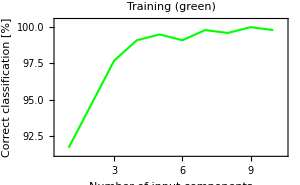

Input component list = {23,28,22,26,21,18,7,11,14,15}

```mathematica
trainingAndTestSet={classificationDataSet,{}};
numberOfInclusionsPerStepList=Table[1,{10}];
perceptronInputComponentRelevanceListForClassification=
	CIP`Perceptron`GetPerceptronInputInclusionClass[
		trainingAndTestSet,
		numberOfHiddenNeurons,
		UtilityOptionsInclusionsPerStep->
			numberOfInclusionsPerStepList];
CIP`Perceptron`ShowPerceptronInputRelevanceClass[
	perceptronInputComponentRelevanceListForClassification]
```

that a subset of 9 components (with indices {23, 28, 22, 26, 21, 18, 7, 11, 14}) already achieves an excellent classification result with the chosen machine learning method. If all other input components are discarded from the data (which leads to a considerably reduced data set)

```mathematica
inputComponentInclusionList={23,28,22,26,21,18,7,11,14};
reducedDataSet=
	CIP`DataTransformation`IncludeInputComponentsOfDataSet[
		classificationDataSet,
		inputComponentInclusionList];
```

and the resulting reduced data set is partitioned in training and test data sets of equal size (again with the optimization heuristics described above but minimum deviation between training and test set predictability as a “best index” criterion)

```mathematica
trainingFraction=0.50;
numberOfTrainingSetOptimizationSteps=100;
blackListLength=20;
perceptronTrainOptimization=
	CIP`Perceptron`GetPerceptronTrainOptimization[
		reducedDataSet,
		numberOfHiddenNeurons,
		trainingFraction,
		numberOfTrainingSetOptimizationSteps,
		UtilityOptionBlackListLength -> blackListLength];

bestOptimization="MinimumDeviation";
bestIndex=CIP`Perceptron`GetBestPerceptronClassOptimization[
	perceptronTrainOptimization,
	UtilityOptionsBestOptimization->bestOptimization];

trainingAndTestSet=perceptronTrainOptimization[[3,bestIndex]];
perceptronInfo=perceptronTrainOptimization[[4,bestIndex]];
```

a convincing class predictor is constructed

```mathematica
CIP`Perceptron`ShowPerceptronClassificationResult[
	{"CorrectClassification"},
	trainingAndTestSet,
	perceptronInfo]
```

Training Set:

98.6% correct classifications

Test Set:

98.6% correct classifications

that achieves a correct classification rate of nearly 99% on both sets. Thus the number of necessary input features may be restricted to the determined subset of only 6 feature out of 30 which may alleviate experimental data set determination.

## Summary

CIP supports data analysis workflows from 2D curve fitting and data smoothing to multi-dimensional clustering and machine learning. The provided high-level functions use corresponding signatures for the various methods available that alleviate method change and analogue data analysis workflows. In addition to the fit methods CIP offers heuristic procedures for additional tasks (like hyper-parameter optimization or training and test set partitioning) as well as standardized diagrams for graphical inspection and methods for model based calculations. The packages may be easily tailored for specific needs or optimized for parallel processing and improved performance.

## References

CIP, version 1.2, for Mathematica 7 or higher is available for download as a ZIP file at http://www.gnwi.de. This website also contains several tutorials with CIP-based data analysis workflows and a CIP user forum for discussion.
CIP, version 1.0, was used for all examples and applications of an introductory textbook recently published: Achim Zielesny, From Curve Fitting to Machine Learning: An illustrative Guide to scientific Data Analysis and Computational Intelligence, Springer: Intelligent Systems Reference Library, Volume 18, Berlin, 2011 (http://dx.doi.org/10.1007/978-3-642-21280-2). This textbook also describes the underlying basics of CIP methods and provides the references to the literature.